```mathematica
α[r_]:=9/2-2/3 Exp[-2r](r^5+9/2 r^4+9 r^3+27/2 r^2+27/2 r+27/4);
```

```mathematica
Series[α[r],{r,∞,3}]
```

9/2+ⅇ^(-2 r+O[1/r]^4) (-(2 r^5)/3-3 r^4-6 r^3-9 r^2-9 r-9/2+O[1/r]^4)

```mathematica
Series[Exp[-2r] r^5,{r,∞,3}]
```

```mathematica
ⅇ^(-2 r+O[1/r]^4) (r^5+O[1/r]^4)
```

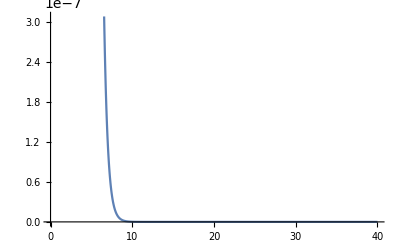

```mathematica
Plot[Exp[-2r]/r,{r,0, 40},PlotRange->Automatic]
```

```mathematica
1/(200*5^2)//N
```

0.0002